# Remnant Configuration Plot Ein hübscher Plot mit Mathematica, der die Remnant-Konfiguration darstellt. 22.Feb 2014, Sven

```mathematica
holo[r_,L_,α_]:=r^2/(r^2 +L^2);
Dholo[r_,L_,α_] = D[holo[r,L,α],r];
halpha[r_,L_,α_] := r^3/(r^α+L^α/2)^(3/α);
Dhalpha[r_,L_,α_] = D[halpha[r,L,α],r];
halphandim[r_,L_,α_,n] := r^(3+n)/(r^α+L^α/2)^((3+n)/α);
```

```mathematica
vorzeichen = -1;
h=holo; Dh=Dholo;
```

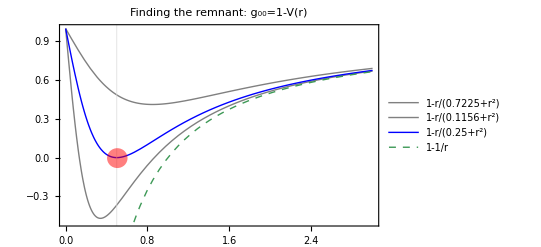

```mathematica
p1=Plot[Evaluate[{
1/r*h[r,0.85,2.24]*vorzeichen+If[vorzeichen==-1,1,0],
1/r*h[r,0.34,2.54]*vorzeichen+If[vorzeichen==-1,1,0],
1/r*h[r,0.5,4.3]*vorzeichen+If[vorzeichen==-1,1,0],
1/r*vorzeichen+If[vorzeichen==-1,1,0]
}],
{r,0,3},
PlotRange-> {1,-.5},
PlotLegends-> "Expressions",
GridLines -> {{0.5},{}},
PlotLabel-> "Finding the remnant: g_00=1-V(r)",
PlotStyle->{GrayLevel[.5],GrayLevel[.5],Blue, Dashed},
Frame->True];
p2=Graphics[{Opacity[0.5],Red, Disk[{0.5,0},{0.1,0.1/1.3}]}];
Show[p1,p2]
```